```mathematica
Clear["Global`*"]
```

```mathematica
rpt[t_]:= ((t+259.67)/2.5967)
```

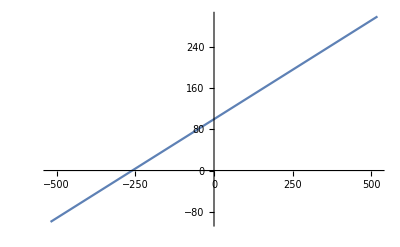

```mathematica
Plot[rpt[t],{t,-519.34,519.34}]
```

```mathematica
u[uges_,r2_,t_]=(r2/((t+259.67)/2.5967))*uges/(1+r2/((t+259.67)/2.5967))
```

(2.5967 r2 uges)/((259.67+t) (1+(2.5967 r2)/(259.67+t)))

```mathematica
u[5,r2,20]
```

(0.0464244 r2)/(1+0.00928487 r2)

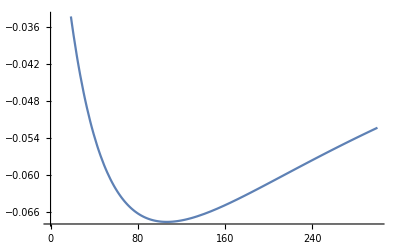

```mathematica
Plot[u[5,r2,25]-u[5,r2,10],{r2,0,300}]
```

```mathematica
u
```

(2.5967 r2 uges)/((259.67+t) (1+(2.5967 r2)/(259.67+t)))

```mathematica
u(t=20)
```

(0.185697 r2 uges)/(1+0.00928487 r2)

```mathematica
u(uges=5)
```

(0.232122 r2)/(1+0.00928487 r2)

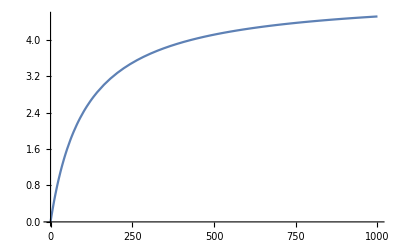

```mathematica
Plot[u,{r2,0,1000}]
```